```mathematica
DimRedMethod[dat_,method_]:=Module[{dat2,dat3,pos,postal,postals,varsites,i,j,countn,keep,dmat,min,col,row,dr,drmat,hmat,rat,rscale},
dat2=Table[StringSplit[dat[[i]],""],{i,1,Length[dat]}];
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="-",dat2[[i,j]]="N"];
];
];
pos=Table[dat2[[;;,i]],{i,1,Length[dat2[[1]]]}];
postal=Table[{i,Tally[pos[[i]]]},{i,1,Length[pos]}];
For[i=1,i<=Length[postal],i++,
postal[[i,2]]=Select[postal[[i,2]],#[[1]]!="N"&];
];
postals=Select[postal,Length[#[[2]]]>1&];
For[i=1,i<=Length[postals],i++,
postals[[i,2]]=Sort[postals[[i,2]],#1[[2]]>#2[[2]]&];
];
varsites=postals[[;;,1]];
(*Print[varsites];*)
(*Convert to string of variant sites*)
For[i=1,i<=Length[dat2],i++,
dat2[[i]]=dat2[[i,varsites]];
];
Print["Pre-binary"];
Print[MatrixForm[dat2]];
drmat=Table[HammingDistance[dat2[[i]],dat2[[j]]],{i,1,Length[dat2]},{j,1,Length[dat2]}];
Print[MatrixForm[drmat]];
(*Convert data to binary data*)
(*Problem with Ns here.  Not always necessarily 0 or 1.  Fix according to the nearest sequence?*)

(*Deal with K nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="K",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"T"]==True&&MemberQ[col[[;;,1]],"G"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"T"]==True&&MemberQ[col[[;;,1]],"G"]==False,dat2[[i,j]]="T"];
If[MemberQ[col[[;;,1]],"T"]==False&&MemberQ[col[[;;,1]],"G"]==True,dat2[[i,j]]="G"];
];
];
];

(*Deal with R nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="R",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"G"]==True&&MemberQ[col[[;;,1]],"A"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"G"]==True&&MemberQ[col[[;;,1]],"A"]==False,dat2[[i,j]]="G"];
If[MemberQ[col[[;;,1]],"G"]==False&&MemberQ[col[[;;,1]],"A"]==True,dat2[[i,j]]="A"];
];
];
];

(*Deal with M nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="M",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"C"]==True&&MemberQ[col[[;;,1]],"A"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"C"]==True&&MemberQ[col[[;;,1]],"A"]==False,dat2[[i,j]]="C"];
If[MemberQ[col[[;;,1]],"C"]==False&&MemberQ[col[[;;,1]],"A"]==True,dat2[[i,j]]="A"];
];
];
];

(*Deal with Y nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="Y",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"C"]==True&&MemberQ[col[[;;,1]],"T"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"C"]==True&&MemberQ[col[[;;,1]],"T"]==False,dat2[[i,j]]="C"];
If[MemberQ[col[[;;,1]],"C"]==False&&MemberQ[col[[;;,1]],"T"]==True,dat2[[i,j]]="T"];
];
];
];

(*Deal with W nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="W",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"A"]==True&&MemberQ[col[[;;,1]],"T"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"A"]==True&&MemberQ[col[[;;,1]],"T"]==False,dat2[[i,j]]="A"];
If[MemberQ[col[[;;,1]],"A"]==False&&MemberQ[col[[;;,1]],"T"]==True,dat2[[i,j]]="T"];
];
];
];

(*Deal with S nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="W",
col=Tally[dat2[[;;,j]]];
If[MemberQ[col[[;;,1]],"G"]==True&&MemberQ[col[[;;,1]],"C"]==True,dat2[[i,j]]="N"];
If[MemberQ[col[[;;,1]],"G"]==True&&MemberQ[col[[;;,1]],"C"]==False,dat2[[i,j]]="G"];
If[MemberQ[col[[;;,1]],"G"]==False&&MemberQ[col[[;;,1]],"C"]==True,dat2[[i,j]]="C"];
];
];
];

(*Deal with H nucleotides: Check for others...*)
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]=="H",
col=Tally[dat2[[;;,j]]];
dat2[[i,j]]="N";
If[MemberQ[col[[;;,1]],"A"]==True&&(MemberQ[col[[;;,1]],"C"]==False&&MemberQ[col[[;;,1]],"T"]==False),dat2[[i,j]]="A"];
If[MemberQ[col[[;;,1]],"C"]==True&&(MemberQ[col[[;;,1]],"A"]==False&&MemberQ[col[[;;,1]],"T"]==False),dat2[[i,j]]="C"];
If[MemberQ[col[[;;,1]],"T"]==True&&(MemberQ[col[[;;,1]],"A"]==False&&MemberQ[col[[;;,1]],"C"]==False),dat2[[i,j]]="T"];
];
];
];

(*Can show corrected..*)
(*Print[dat2];
Print[postals];*)
(*Perhaps change to a 2 then fix afterwards?*);
(*This code goes by the overall consensus.  Instead use the first sequence to specify variation?*);
For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
If[dat2[[i,j]]==postals[[j,2,1,1]],dat2[[i,j]]=0,
If[dat2[[i,j]]=="N",dat2[[i,j]]=2,
dat2[[i,j]]=1];
];
];
];
(*Print["I am here"];
Print[dat2];*)
countn=N[Table[Length[Select[dat2[[i]],#==2&]],{i,1,Length[dat2]}]/Length[dat2[[1]]]];
Print[countn];
countn=Partition[Riffle[Range[Length[dat2]],countn],2];
keep=Select[countn,#[[2]]<=0.1&][[;;,1]];
Print[keep];
dat2=dat2[[keep]];

Print[MatrixForm[dat2]];

(*Reduce sequences so that nothing is equal to 2*)
dat3=dat2;
For[i=1,i<=Length[dat3],i++,
dat3[[i]]=Partition[Riffle[Range[Length[dat3[[i]]]],dat3[[i]]],2];
dat3[[i]]=Select[dat3[[i]],#[[2]]==2&];
dat3[[i]]=dat3[[i,;;,1]];
];
dat3=DeleteDuplicates[Flatten[dat3]];
keep=Select[Range[Length[dat2[[1]]]],MemberQ[dat3,#]==False&];

dat3=dat2;
For[i=1,i<=Length[dat3],i++,
dat3[[i]]=dat3[[i,keep]];
];

dmat=Table[Total[Table[Abs[dat3[[i,k]]-dat3[[j,k]]],{k,1,Length[dat3[[i]]]}]],{i,1,Length[dat3]},{j,1,Length[dat3]}];
(*Print[MatrixForm[dmat]];*)

For[i=1,i<=Length[dat2],i++,
For[j=1,j<=Length[dat2[[i]]],j++,
(*Check if this equals 2*)
If[dat2[[i,j]]==2,
(*Print[{i,j}];*)
(*Look at dmat[[i]].  Which vectors are nearest to this given dmat*)
keep=Select[Range[Length[dmat[[i]]]],#!=i&];
(*Print[keep];
Print[dmat[[i,keep]]];*)
min=Min[dmat[[i,keep]]];
(*Print[{"Min",min}];*)
row=Partition[Riffle[keep,dmat[[i,keep]]],2];
row=Select[row,#[[2]]==min&][[;;,1]];
(*Print[{i,j,row}];*)
(*Look at element j of these cases*)
dat2[[i,j]]=N[Mean[dat2[[row,j]]]];

];
];
];

(*Note: There is a kind of smoothing here.  In replacing a variant we find a set of close-by sequences then put in the proportion of sequences that have a variant at the unknown nucleotide.  Might need to think about the consequences of this?  It's a kind of interpolation...*)

(*Print["Now here"];
Print[dat2];*)
Print[dat2];

dr=DimensionReduce[dat2,Method->method];
(*Print[dat3];*)
drmat=Table[EuclideanDistance[dr[[i]],dr[[j]]],{i,1,Length[dr]},{j,1,Length[dr]}];
(*Print[MatrixForm[drmat]];*)
hmat=Table[Total[Table[Abs[dat2[[i,k]]-dat2[[j,k]]],{k,1,Length[dat2[[i]]]}]],{i,1,Length[dat2]},{j,1,Length[dat2]}];
Print[MatrixForm[hmat]];
rat=Partition[Riffle[Flatten[drmat],Flatten[hmat]],2];
Print[rat];
rscale=Total[rat[[;;,2]]]/Total[rat[[;;,1]]];
(*Print[MatrixForm[drmat]];
Print[MatrixForm[hmat]];
Print["Scale"];
Print[rscale];
Print[dr];*)
dr=dr*rscale;
Print[{"Scale",rscale}];
drmat=Table[EuclideanDistance[dr[[i]],dr[[j]]],{i,1,Length[dr]},{j,1,Length[dr]}];
Print[MatrixForm[drmat]];
(*Print[dat3];
Print[dat2];
Print[keep];*)
Return[dr];
];

CalcDist[dat_,i_,j_]:=Module[{s1,s2,d},
s1=StringSplit[dat[[i]],""];
s2=StringSplit[dat[[j]],""];
d=Select[Partition[Riffle[s1,s2],2],#[[1]]!="N"&&#[[2]]!="N"&&#[[1]]!="-"&&#[[2]]!="-"&&#[[1]]!=#[[2]]&];
d=Length[d];
Return [d];
];

oneParamChartStyle={RGBColor["#4477AA"]};
twoParamChartStyle={RGBColor["#4477AA"],RGBColor["#CC6677"]};
threeParamChartStyle={RGBColor["#4477AA"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
fourParamChartStyle={RGBColor["#4477AA"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
fiveParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
sixParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"],RGBColor["#AA4499"]};
sevenParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"],RGBColor["#AA4499"]};
eightParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#CC6677"],RGBColor["#AA4499"]};
nineParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#CC6677"],RGBColor["#882255"],RGBColor["#AA4499"]};
tenParamChartStyle={RGBColor["#4477AA"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#661100"],RGBColor["#CC6677"],RGBColor["#882255"],RGBColor["#AA4499"]};
elevenParamChartStyle={RGBColor["#4477AA"],RGBColor["#6699CC"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#661100"],RGBColor["#CC6677"],RGBColor["#882255"],RGBColor["#AA4499"]};
twelveParamChartStyle={RGBColor["#4477AA"],RGBColor["#6699CC"],RGBColor["#88CCEE"],RGBColor["#44AA99"],RGBColor["#117733"],RGBColor["#999933"],RGBColor["#DDCC77"],RGBColor["#661100"],RGBColor["#CC6677"],RGBColor["#AA4466"],RGBColor["#882255"],RGBColor["#AA4499"]};
twelveParamChartStyle=Join[twelveParamChartStyle,Lighter[twelveParamChartStyle]];
```

```mathematica
s=27;
SetDirectory["/Users/chris/Documents/Projects/MPhil_WithinHost/Writeup/Simulations"];
dat=Import["/Users/chris/Documents/Projects/MPhil_WithinHost/Writeup/Simulations/Rate02/Split1/Sim"<>ToString[s]<>"/PopSeqs.dat"];
times=Flatten[Import["/Users/chris/Documents/Projects/MPhil_WithinHost/Writeup/Simulations/Rate01/Split1/Sim"<>ToString[s]<>"/Times.in"]];
dat=Flatten[dat[[2;;-1;;2]]];
out=Import["/Users/chris/Documents/Projects/MPhil_WithinHost/Writeup/Simulations/Rate02/Split1/Sim"<>ToString[s]<>"/Output_points2.dat"];
sets=Import["/Users/chris/Documents/Projects/MPhil_WithinHost/Writeup/Simulations/Rate02/Split1/Sim"<>ToString[s]<>"/Subsets.out","Table"];
(*dat=dat[[;;-1;;2]];
dat=Flatten[dat];
times=Flatten[times]*)
```

```mathematica
dr=DimRedMethod[dat,"PrincipalComponentsAnalysis"]
```

Pre-binary

(C | T | G | C
C | A | G | C
C | T | G | C
C | T | T | C
C | T | T | G
G | T | T | C
G | T | T | C)

(0 | 1 | 0 | 1 | 2 | 2 | 2
1 | 0 | 1 | 2 | 3 | 3 | 3
0 | 1 | 0 | 1 | 2 | 2 | 2
1 | 2 | 1 | 0 | 1 | 1 | 1
2 | 3 | 2 | 1 | 0 | 2 | 2
2 | 3 | 2 | 1 | 2 | 0 | 0
2 | 3 | 2 | 1 | 2 | 0 | 0)

{0.,0.,0.,0.,0.,0.,0.}

{1,2,3,4,5,6,7}

(0 | 0 | 1 | 0
0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

{{0,0,1,0},{0,1,1,0},{0,0,1,0},{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0}}

(0 | 1 | 0 | 1 | 2 | 2 | 2
1 | 0 | 1 | 2 | 3 | 3 | 3
0 | 1 | 0 | 1 | 2 | 2 | 2
1 | 2 | 1 | 0 | 1 | 1 | 1
2 | 3 | 2 | 1 | 0 | 2 | 2
2 | 3 | 2 | 1 | 2 | 0 | 0
2 | 3 | 2 | 1 | 2 | 0 | 0)

{{0.,0},{2.16804,1},{0.,0},{1.89933,1},{4.45413,2},{3.7632,2},{3.7632,2},{2.16804,1},{0.,0},{2.16804,1},{4.06489,2},{6.25889,3},{5.66825,3},{5.66825,3},{0.,0},{2.16804,1},{0.,0},{1.89933,1},{4.45413,2},{3.7632,2},{3.7632,2},{1.89933,1},{4.06489,2},{1.89933,1},{0.,0},{3.38072,1},{2.36501,1},{2.36501,1},{4.45413,2},{6.25889,3},{4.45413,2},{3.38072,1},{0.,0},{5.10732,2},{5.10732,2},{3.7632,2},{5.66825,3},{3.7632,2},{2.36501,1},{5.10732,2},{0.,0},{0.,0},{3.7632,2},{5.66825,3},{3.7632,2},{2.36501,1},{5.10732,2},{0.,0},{0.,0}}

{Scale,0.471689}

(0. | 1.02264 | 0. | 0.895893 | 2.10096 | 1.77506 | 1.77506
1.02264 | 0. | 1.02264 | 1.91736 | 2.95225 | 2.67365 | 2.67365
0. | 1.02264 | 0. | 0.895893 | 2.10096 | 1.77506 | 1.77506
0.895893 | 1.91736 | 0.895893 | 0. | 1.59465 | 1.11555 | 1.11555
2.10096 | 2.95225 | 2.10096 | 1.59465 | 0. | 2.40906 | 2.40906
1.77506 | 2.67365 | 1.77506 | 1.11555 | 2.40906 | 0. | 0.
1.77506 | 2.67365 | 1.77506 | 1.11555 | 2.40906 | 0. | 0.)

{{0.630603,0.0122805},{1.63443,0.207521},{0.630603,0.0122805},{-0.258614,-0.0968928},{-0.670289,-1.63748},{-0.983368,0.75115},{-0.983368,0.75115}}

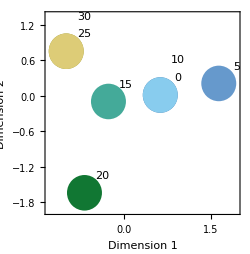

```mathematica
Show[Table[Graphics[{twelveParamChartStyle[[i]],Disk[dr[[i]],0.3]}],{i,1,Length[dr]}],Table[Graphics[Text[ToString[times[[i]]],dr[[i]]+{0.3,0.3}]],{i,sets[[;;,1]]+1}],Table[Graphics[Text[ToString[times[[i]]],dr[[i]]+{0.3,0.6}]],{i,Select[sets,Length[#]>1&][[;;,2]]+1}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,FontSize->10],FrameLabel->{{"Dimension 2",None},{"Dimension 1","Sim"}},ImageSize->250]
```

```mathematica
?Dendrogram
```

```mathematica
ClusteringTree[{{0,0,1,0},{0,1,1,0},{0,0,1,0},{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0}}]
```

There is an underlying question here of which changes represent error in the sequence and which represent genuine patterns of evolution.  Given a mid-time point that is different from the others by one, we can model that as an error.  If it is different by too many that gets problematic.

What is the right approach here?  What if we hand-draw a tree of these sequences, thinking about how a tree might be reconstructed.

Infinite sites assumption means that a novel sequence is either in line with everything else, or an independent branch that happened from the beginning (under our current model).  Can we separate out these weird cases in the case that they share some variants with everything else?  Assumption of k continuous populations plus a known error term?

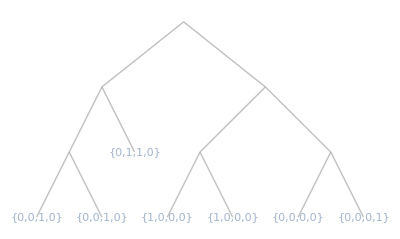

```mathematica
out
```

{{0.694275,0.134949},{1.70828,0.331208},{0.694275,0.134949},{-0.353566,-0.0841165},{-1.15989,0.830363},{-0.871328,-1.08186},{-0.871328,-1.08186}}

```mathematica
Select[sets,Length[#]>1&][[;;,2]]
```

```mathematica
Select[sets,Length[#]>1&][[;;,2]]
```

```mathematica
sets[[;;,1]]
```

```mathematica
Table[i,{i,sets[[;;,1]]}]
```

{0,1,3,4,5}

```mathematica
Length[times]
```

7

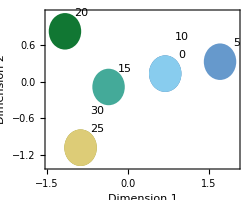

```mathematica
Show[Table[Graphics[{twelveParamChartStyle[[i]],Disk[out[[i]],0.3]}],{i,1,Length[out]}],Table[Graphics[Text[ToString[times[[i]]],out[[i]]+{0.3,0.3}]],{i,sets[[;;,1]]+1}],Table[Graphics[Text[ToString[times[[i]]],out[[i]]+{0.3,0.6}]],{i,Select[sets,Length[#]>1&][[;;,2]]+1}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,FontSize->10],FrameLabel->{{"Dimension 2",None},{"Dimension 1","Sim"}},ImageSize->250]
```

```mathematica
|
```

```mathematica
MatrixForm[{{0,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0},{0,0,1,0,1,1,0,0,0},{0,0,1,1,1,1,1,0,1}}]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1)

```mathematica
|
```

```mathematica
times
```

{{0},{5},{10},{15},{20},{25}}

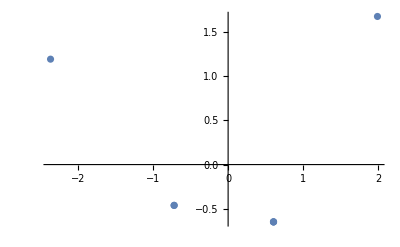

```mathematica
ListPlot[DimensionReduce[N[{{1,1,0},{1,0,0},{1,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}}]]]
```

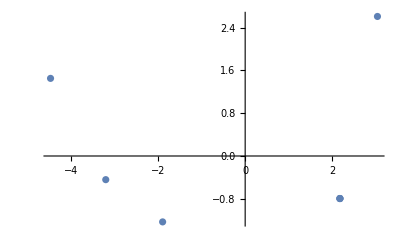

```mathematica
ListPlot[DimensionReduce[N[{{"C","G","C","C","C","C"},{"C","C","C","C","C","C"},{"C","C","C","C","C","C"},{"C","C","C","C","C","C"},{"G","C","C","G","G","C"},{"G","C","C","G","G","G"},{"G","C","G","G","G","G"}}]]]
```

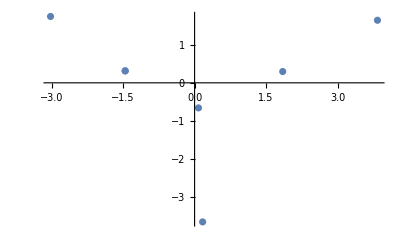

```mathematica
ListPlot[DimensionReduce[{{"T","T","C","T","T"},{"T","A","C","T","T"},{"T","A","C","T","A"},{"T","A","C","A","A"},{"A","A","C","T","A"},{"A","A","C","T","A"},{"A","A","G","T","A"}}]]
```

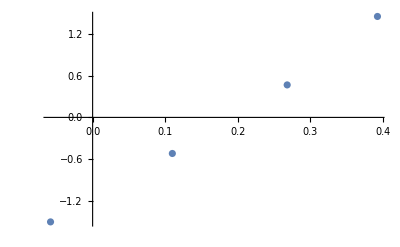

```mathematica
ListPlot[{{0.392902, 1.45528},{0.268376 ,0.468485},{0.109956,-0.520062},{-0.0580541,-1.50631}}]
```

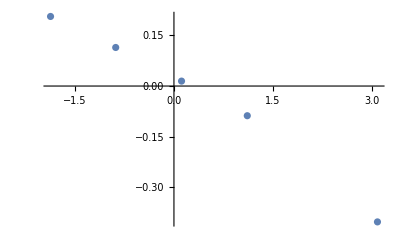

```mathematica
ListPlot[{{-1.8718 ,0.206111},{-0.883367, 0.114214},{0.115072, 0.0146279},{1.11239,-0.0879256},{3.08695,-0.402457}}]
```

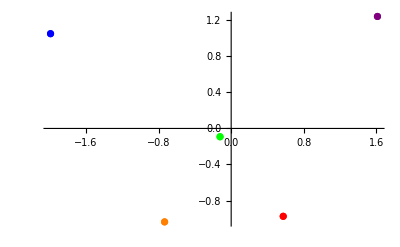

```mathematica
ListPlot[{{{0.573395,-0.97538}},{{-0.733531,-1.03739}},{{-0.122619,-0.0923265}},{{-1.98993, 1.0519}},{{1.61155, 1.24322}}},PlotStyle->{Red,Orange,Green,Blue,Purple}]
```